# KerrImages

The KerrImages` package provides functions for generating images without the need to use the specific functions of the other two packages. The public functions in this package are:

DiskImage[a, θo, α, m, mdot, imageSize, maxBardeenCoordinate] | returns a list containing tables with information specified by the option 'Output'->{'information1', 'information2', ...}. Geodesics are specified by (dimensionless) a, θo (distant observer's θ) and maximal Bardeen coordinate that is shown. The number of geodesics to be generated is specified in imageSize in the form {xsize, ysize}. Disk is specified by BH mass m (in solar mass by default), matter inflow mdot and parameter α (both in Shakura & Sunyaev definition by default).
DiskImageFromTemplate[file, a, α, m, mdot] | returns a list containing tables with information specified by the option 'Output'->{'information1', 'information2', ...}. Template is passed in file. Disk is specified by BH mass m, and spin parameter  a  matter inflow mdot and parameter α (both in Shakura & Sunyaev definition by default).
GenerateTemplate[directory, name, a, θo, imageSize, maxBardeenCoordinates] | generates a template containing information about null geodesics specified by (dimensionless) a, θo (distant observer's θ) and maximal Bardeen coordinate that is shown. The number of geodesics to be generated is specified in imageSize in the form {xsize, ysize}. The template is saved in directory/name.mx file, which can be used later with DiskImageFromTemplate.
StellarBackgroundFromTemplate[templateFile, θo,imageFile, angle, Ratio_:0.8, bgColor_:{0.,0.,0.}] | generates an image of stellar background given by imageFile distorted by geometry given by the template stored in templateFile and θo. The image's part Ratio (default is 0.8) spans angle on the celestial sphere. The background color can be specified in bgColor as RGB list of size 3 (default is black).

First, load the paclet:

```mathematica
Needs["BlackHoleImages`"]
```

The DiskImage function provides the easiest way of generating an accretion disk image in the package. It takes the following arguments:

a | The spin parameter of the black hole.
θo | The observer's θ coordinate.
α | The efficiency of angular momentum transport in the disk α as defined by Shakura and Sunyaev.
m | The mass of the black hole.
mdot | The mass influx.
imageSize | A list of length 2 specifing the size of the image in pixels.
maxBardeenCoordinate | The maximal Bardeen's coordinate (for definition see the KerrNullGeodesics tutorial).

Additional options can be given:

Option | Default | Description
"InputUnits" | "NovikovThorne" | This option specifies the units in which the user has provided the input. The default option is "InputUnits"->"NovikovThorne", which expects the mass M to be given in geometrized units and the mass influx mdot to be dimensionless, ṁ := Ṁ /1014 kg /s. Other accepted options are "InputUnits"->"SI", "InputUnits"->"CGS", and "InputUnits"->"ShakuraSunyaev", the first two expecting SI and CGS units respectively, the last one expecting M to be given in solar masses and mdot to be given in multiples of the critical mass influx; the mass influx at which the Eddington luminosity  is reached.
"OutputUnits" | "SI" | This option changes the units of the output functions (temperature and flux density). As of June 2024, only the default option "OutputUnits"->"SI" is supported.
"rUnits" | "BHMass" | The output functions of DiskParams are functions of radius. This option changes the units of radius these functions expect. The default option is "rUnits"->"BHMass", which expects the dimensionless r used throughout chapters 1 and 2, r = Rc2/(GM), where R is radius with dimension. Other supported options are "rUnits"->"SI", "rUnits"->"CGS", and "rUnits"->"ShakuraSunyaev", the first two using the meters and centimeters as units respectively, and the last one using Shakura and Sunyaev’s definition, r = Rc^2/(6GM) .
"Grid" | True | Specifies whether a grid of lines of constant r and φ should be generated over the data. Takes a boolean value.
"Rotation" | "Counterclockwise" | Sets the direction of rotation of the black hole. The default option is "Rotation"-> "Counterclockwise".  The opposite is "Rotation"-> "Clockwise".
"PhiRange" | {-Pi, Pi} | Sets the range of output of the azimuthal angle. The default is "PhiRange"-> {−π, π}, which starts the coordinate at 0 and does not take the modulus of it after full windings. Typical options could be {−∞, ∞}
or {0, 2π}, but other option values in the format {bottomvalue, topvalue} are valid as well.
"Output" | {MaximalFrequency} |  Takes the list of keys to the association returned by the ObservedDiskElement function. The output will be a list of matrices with values corresponding to these keys. The default option is "Output"->{"MaximalFrequency"}.

Let us use this function to generate an image of an accretion disk with efficiency α=0.1, and the mass influx 10^14 kg/s. We choose the black hole's mass to be 3 times the solar mass and its spin parameter a=0.8. The observer's  θ coordinate shall be θo=π/4. The maximal Bardeen coordinate is 10 and, for demonstrative purposes, let us only generate a 100x100 pixels image. We generate the physical temperature of the disk and do not show the coordinate grid. The function DiskImage returns an array of matrices with the requested data (i.e. physical temperature, maximal frequency, etc.), so when plotting the data, we need to specify the position of the matrix we wish to plot (in our example, we only generate a single matrix).

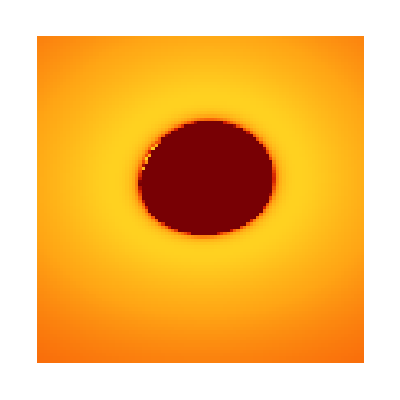

```mathematica
img = DiskImage[0.8, π/4, 0.1, 3 1500, 1, {100, 100}, 10,  "Grid"->False,"Output"->{"PhysicalTemperature"}];
ArrayPlot[Reverse[img[[1]]], ColorFunction->"SolarColors"]
```

As can be seen, the DiskImage function is really simple to use, however for higher resolution, the time to generate an image may be quite large. The larger part of the time is due to the geodesic generation. For this reason we work in this package with so called templates, i. e. objects which store the relevant information about the geodesics associated with each pixel of the image to be generated, which can be saved and reused to generate multiple images of different disks in the same geometry and viewed under the same angle. We thus introduce the GenerateTemplate function, which takes the following arguments:

directory | The path string to a directory where the template should be stored.
name | The name of the file in which the template should be stored.
a | The spin parameter of the black hole.
θo | The observer's θ coordinate.
imageSize | A list of length 2 specifing the size of the image in pixels.
maxBardeenCoordinate | The maximal Bardeen's coordinate (for definition see the KerrNullGeodesics tutorial).

Additional options can be given:

Option | Default | Description
"Rotation" | "Counterclockwise" | Sets the direction of rotation of the black hole. The default option is "Rotation"-> "Counterclockwise".  The opposite is
"Rotation"-> "Clockwise".
"PhiRange" | {-Pi, Pi} | Sets the range of output of the azimuthal angle. The default is "PhiRange"-> {−∞, ∞}, which starts the coordinate at 0 and does not take the modulus of it after full windings. Typical options could be {−π, π}
or {0, 2π}, but other option values in the format {bottomvalue, topvalue} are valid as well.

The function generates a template and saves it the the directory directory as a file called name.mx.

Let us generate a template for the same situation as in the previous example for the DiskImage function:

```mathematica
GenerateTemplate[Directory[], "template_a0.8_th0.25pi_size100x100_mBC10", 0.8,  π/4, {100, 100}, 10]
```

%

The final image of the disk is then generated using the DiskImageFromTemplate function. It takes the following arguments:

file | The path to the template from which the image should be generated.
a | he spin parameter of the black hole.
α | The efficiency of angular momentum transport in the disk α as defined by Shakura and Sunyaev.
m | The mass of the black hole.
mdot | The mass influx.

The following options can be given:

Option | Default | Description
"InputUnits" | "NovikovThorne" | This option specifies the units in which the user has provided the input. The default option is "InputUnits"->"NovikovThorne", which expects the mass M to be given in geometrized units and the mass influx
mdot to be dimensionless, ṁ := Ṁ /1014 kg /s. Other accepted options are "InputUnits"->"SI", "InputUnits"->"CGS", and "InputUnits"->"ShakuraSunyaev", the first two expecting SI and CGS units respectively, the last one expecting M to be given in solar masses and mdot to be given in multiples of the critical mass influx; the mass influx at which the Eddington luminosity  is reached.
"OutputUnits" | "SI" | This option changes the units of the output functions (temperature and flux density). As of June 2024, only the default option "OutputUnits"->"SI" is supported.
"rUnits" | "BHMass" | The output functions of DiskParams are functions of radius. This option changes the units of radius these functions expect. The default option is "rUnits"->"BHMass", which expects the dimensionless r used throughout chapters 1 and 2, r = Rc2/(GM), where R is radius with dimension. Other supported options are "rUnits"->"SI", "rUnits"->"CGS", and "rUnits"->"ShakuraSunyaev", the first two using the meters and centimeters as units respectively, and the last one using Shakura and Sunyaev’s definition, r = Rc^2/(6GM) .
"Grid" | True | Specifies whether a grid of lines of constant r and φ should be generated over the data. Takes a boolean value.
"Output" | {MaximalFrequency} | Takes the list of keys to the association returned by the ObservedDiskElement function. The output will be a list of matrices with values corresponding to these keys. The default option is 
"Output"->{"MaximalFrequency"}.

With the template generated in the previous example, we can easily generate the image of the disk with the parameters we used in the example on the DiskImage function:

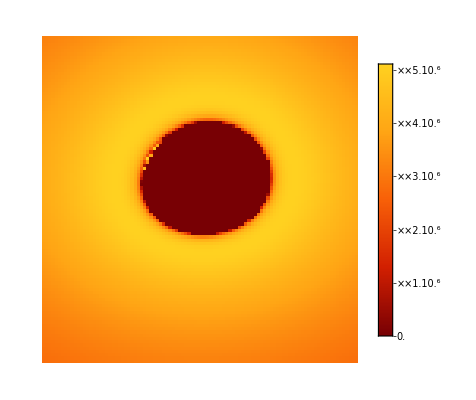

```mathematica
img1 = DiskImageFromTemplate[Directory[]<>"\\template_a0.8_th0.25pi_size100x100_mBC10.mx",0.8, 0.1,3 1500, 1, "Grid"->False,"Output"->{"PhysicalTemperature"}];
ArrayPlot[Reverse[img1[[1]]],  ColorFunction->"SolarColors", PlotLegends->Automatic]
```

Or we might choose to examine, for example, the disk forming near a black hole 10 times more massive, with 100 times smaller matter influx:

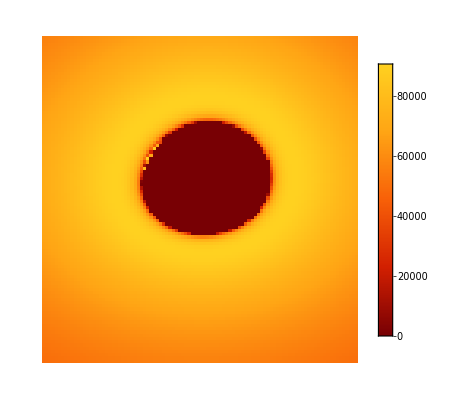

```mathematica
img2 = DiskImageFromTemplate[Directory[]<>"\\template_a0.8_th0.25pi_size100x100_mBC10.mx",0.8, 0.1,30 1500, 0.00001, "Grid"->False,"Output"->{"PhysicalTemperature"}];
ArrayPlot[Reverse[img2[[1]]],  ColorFunction->"SolarColors", PlotLegends->Automatic]
```

The templates can also be used to generate an image distorted by the black hole's gravity using the StellarBackgroundFromTemplate function. We imagine, that the background is very far away from the black hole. The arguments of the function are:

templateFile | The path to the template from which the image should be generated.
θo | The observer's θ coordinate.
imageFile | The path to the undistorted image.
angle |  The angle of the original image on the celestial sphere. 
Ratio | The ratio between the angle on the celestial sphere  of the generated image and the original one (set to 0.8 by default). 
bgColor | The background color given as a list of length three corresponding to the colors RGB code, which should be used whenever the geodesic for a given pixel does not end in the range of the original image (set to {0.,0.,0.} by default).

As an example, let us generate the image of the Sombrero Galaxy (M104) distorted by a template similar to the one generated while demonstrating the GenerateTemplate function, only with larger maxBardeenCoordinate and 200x100 pixels resolution:

```mathematica
GenerateTemplate[Directory[], "template_a0.8_th0.25pi_size200x100_mBC400", 0.8,  π/4, {200, 100}, 401]
```

%

The original image taken by Hubble Space Telescope:

```mathematica
Import[Directory[]<>"\galaxy.jpg"]
```

-Graphics-

For the distorted image, we set the angle on the celestial sphere to π/6:

```mathematica
img3 = StellarBackgroundFromTemplate[Directory[]<>"\\template_a0.8_th0.25pi_size200x100_mBC400.mx",  π/4, Directory[]<>"\\galaxy.jpg", π/6];
Image[img3]
```

-Graphics-

Related Guides

KerrImages

Related Tech Notes

KerrNullGeodesics

AlphaDiskModel

## Metadata

### Categorization

Tech Note

BlackHoleImages

BlackHoleImages`

BlackHoleImages/tutorial/KerrImages

### Keywords